## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGK";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PGK_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  | 
1 | 3pg | Null
atp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  | 
1 | 3pg | Null
atp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGK[c] + 13dpg[c] <=> E_PGK[c]&13dpg",
				"E_PGK[c]&13dpg + adp[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c] + adp[c] <=> E_PGK[c]&adp",
				"E_PGK[c]&adp + 13dpg[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp",

				"E_PGK[c]&3pg&atp <=> E_PGK[c]&3pg + atp[c]",
				"E_PGK[c]&3pg <=> E_PGK[c] + 3pg[c]",
				
				"E_PGK[c]&3pg&atp <=> E_PGK[c]&atp + 3pg[c]",
				"E_PGK[c]&atp <=> E_PGK[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1,((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2,((PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c)^PGK3,((PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c)^PGK4,((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5,((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c)^PGK7,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c)^PGK8,((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet2={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSet3={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9,  Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet4={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2, catalyticReactionsSet3, catalyticReactionsSet4};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGK^c&(13dpg)^c&adp^c)_^-((PGK^c&(3pg)^c&atp^c)_^)/K_PGK9) Volume_c k_PGK9^⟶}

Volume_c (-(PGK^c&(3pg)^c&atp^c)_^ k_PGK9^⟵+(PGK^c&(13dpg)^c&adp^c)_^ k_PGK9^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	adp[c]	atp[c]	3pg[c]	param_PGK_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	1	8.500000000000002e-6	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.09090909090909091
1	1	0.000013471592135919474	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.13680688860321008
1	1	0.000021351034667831454	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.20076000891310192
1	1	0.000033839109497047245	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.2847472489508013
1	1	0.00005363137428081642	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.3868631798468569
1	1	0.00008500000000000002	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.5000000000000001
1	1	0.00013471592135919474	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.6131368201531432
1	1	0.00021351034667831454	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.7152527510491988
1	1	0.00033839109497047284	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.7992399910868982
1	1	0.0005363137428081642	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.86319311139679
1	1	0.0008500000000000003	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.9090909090909092
1	1.100000000000001e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.09090909090909097
1	1.7433825117072269e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.13680688860321014
1	2.7630750746605424e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.200760008913102
1	4.37917887608847e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.2847472489508014
1	6.940530789282128e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.38686317984685703
1	0.000011000000000000008	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.5000000000000002
1	0.00001743382511707227	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.6131368201531434
1	0.000027630750746605424	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.7152527510491988
1	0.00004379178876088469	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.7992399910868982
1	0.00006940530789282128	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.8631931113967901
1	0.00011000000000000009	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.9090909090909092
1	0	0	0.00035000000000000005	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.09090909090909091
1	0	0	0.0005547126173613899	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.13680688860321005
1	0	0	0.000879160251028353	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.20076000891310175
1	0	0	0.0013933750969372409	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.28474724895080145
1	0	0	0.0022083507056806758	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.38686317984685686
1	0	0	0.0035	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.5
1	0	0	0.0055471261736139	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.6131368201531431
1	0	0	0.008791602510283538	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.7152527510491987
1	0	0	0.013933750969372407	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.7992399910868984
1	0	0	0.022083507056806766	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.8631931113967901
1	0	0	0.035	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.9090909090909091
1	0	0	1	0.00024999999999999995	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.0909090909090909
1	0	0	1	0.0003962232981152784	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.13680688860321003
1	0	0	1	0.0006279716078773948	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.20076000891310167
1	0	0	1	0.0009952679263837431	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.2847472489508014
1	0	0	1	0.0015773933612004821	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.3868631798468568
1	0	0	1	0.002499999999999999	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.4999999999999999
1	0	0	1	0.0039622329811527844	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.6131368201531431
1	0	0	1	0.006279716078773954	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.7152527510491987
1	0	0	1	0.00995267926383743	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.7992399910868982
1	0	0	1	0.01577393361200483	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.8631931113967901
1	0	0	1	0.024999999999999994	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.9090909090909092
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateFor_13dpg.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateFor_adp.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateRev_atp.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateFor_13dpg.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateFor_adp.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateRev_atp.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.684698004016862
best_fit: 0.9858531885517386
best_fit: 4.670542202081233
best_fit: 0.601082869237858
best_fit: 1.2654177317705837
best_fit: 5.961599093867536
best_fit: 1.0989387845032355
best_fit: 1.0910878072969172
best_fit: 7.101939910193852
best_fit: 4.229528739327221

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\PGK_PGK.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_1 | 4.29975×10^-8 | 1.84879×10^-15 | 0.00018811 | 9.90054×10^-6 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_2 | 4.64557×10^-8 | 2.15813×10^-15 | 0.00020324 | 0.0000106968 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_3 | 9.5906×10^-8 | 9.19796×10^-15 | 0.00041958 | 0.0000220832 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | haldaneRatio_4 | 1.85359×10^-7 | 3.4358×10^-14 | 0.00081093 | 0.0000426805 | 1900 | 1900.
1 | relRateFor_adp | 0.0000137046 | 1.87815×10^-10 | 2.86867×10^-6 | 0.00315554 | 0.0909091 | 0.0909062
1 | relRateFor_adp | 0.0000111489 | 1.24297×10^-10 | 3.51196×10^-6 | 0.00256709 | 0.136807 | 0.136803
1 | relRateFor_adp | 7.58781×10^-6 | 5.75749×10^-11 | 3.50756×10^-6 | 0.00174714 | 0.20076 | 0.200757
1 | relRateFor_adp | 2.91116×10^-6 | 8.47487×10^-12 | 1.90871×10^-6 | 0.000670318 | 0.284747 | 0.284745
1 | relRateFor_adp | 2.77501×10^-6 | 7.70069×10^-12 | 2.47195×10^-6 | 0.000638972 | 0.386863 | 0.386866
1 | relRateFor_adp | 9.07496×10^-6 | 8.23548×10^-11 | 0.000010448 | 0.00208961 | 0.5 | 0.50001
1 | relRateFor_adp | 0.000015375 | 2.3639×10^-10 | 0.0000217068 | 0.00354029 | 0.613137 | 0.613159
1 | relRateFor_adp | 0.0000210614 | 4.43583×10^-10 | 0.0000346875 | 0.00484969 | 0.715253 | 0.715287
1 | relRateFor_adp | 0.0000257384 | 6.62463×10^-10 | 0.0000473682 | 0.00592665 | 0.79924 | 0.799287
1 | relRateFor_adp | 0.0000292997 | 8.58474×10^-10 | 0.0000582374 | 0.00674674 | 0.863193 | 0.863251
1 | relRateFor_adp | 0.0000318557 | 1.01478×10^-9 | 0.0000666846 | 0.00733531 | 0.909091 | 0.909158
1 | relRateFor_13dpg | 2.75336×10^-6 | 7.58097×10^-12 | 5.76347×10^-7 | 0.000633982 | 0.0909091 | 0.0909085
1 | relRateFor_13dpg | 2.37316×10^-6 | 5.63186×10^-12 | 7.47564×10^-7 | 0.000546438 | 0.136807 | 0.136806
1 | relRateFor_13dpg | 1.84339×10^-6 | 3.39808×10^-12 | 8.52136×10^-7 | 0.000424455 | 0.20076 | 0.200759
1 | relRateFor_13dpg | 1.14767×10^-6 | 1.31714×10^-12 | 7.52471×10^-7 | 0.000264259 | 0.284747 | 0.284746
1 | relRateFor_13dpg | 3.01768×10^-7 | 9.1064×10^-14 | 2.68811×10^-7 | 0.0000694847 | 0.386863 | 0.386863
1 | relRateFor_13dpg | 6.35425×10^-7 | 4.03764×10^-13 | 7.3156×10^-7 | 0.000146312 | 0.5 | 0.500001
1 | relRateFor_13dpg | 1.57262×10^-6 | 2.47313×10^-12 | 2.22023×10^-6 | 0.00036211 | 0.613137 | 0.613139
1 | relRateFor_13dpg | 2.41852×10^-6 | 5.84925×10^-12 | 3.98315×10^-6 | 0.000556887 | 0.715253 | 0.715257
1 | relRateFor_13dpg | 3.11425×10^-6 | 9.69856×10^-12 | 5.73123×10^-6 | 0.000717086 | 0.79924 | 0.799246
1 | relRateFor_13dpg | 3.64402×10^-6 | 1.32789×10^-11 | 7.24281×10^-6 | 0.000839071 | 0.863193 | 0.8632
1 | relRateFor_13dpg | 4.02423×10^-6 | 1.61944×10^-11 | 8.4238×10^-6 | 0.000926618 | 0.909091 | 0.909099
1 | relRateRev_atp | 0.000609123 | 3.7103×10^-7 | 0.000127416 | 0.140157 | 0.0909091 | 0.0907817
1 | relRateRev_atp | 0.000494896 | 2.44922×10^-7 | 0.000155808 | 0.113889 | 0.136807 | 0.136651
1 | relRateRev_atp | 0.000335692 | 1.12689×10^-7 | 0.000155119 | 0.077266 | 0.20076 | 0.200605
1 | relRateRev_atp | 0.000126544 | 1.60134×10^-8 | 0.0000829572 | 0.0291336 | 0.284747 | 0.284664
1 | relRateRev_atp | 0.000127846 | 1.63446×10^-8 | 0.0001139 | 0.029442 | 0.386863 | 0.386977
1 | relRateRev_atp | 0.000409789 | 1.67927×10^-7 | 0.000472009 | 0.0944018 | 0.5 | 0.500472
1 | relRateRev_atp | 0.000691764 | 4.78538×10^-7 | 0.000977411 | 0.159412 | 0.613137 | 0.614114
1 | relRateRev_atp | 0.000946154 | 8.95207×10^-7 | 0.00155995 | 0.218097 | 0.715253 | 0.716813
1 | relRateRev_atp | 0.00115501 | 1.33404×10^-6 | 0.00212841 | 0.266304 | 0.79924 | 0.801368
1 | relRateRev_atp | 0.00131328 | 1.7247×10^-6 | 0.00261419 | 0.302851 | 0.863193 | 0.865807
1 | relRateRev_atp | 0.00142554 | 2.03217×10^-6 | 0.00298893 | 0.328783 | 0.909091 | 0.91208
1 | relRateRev_3pg | 0.000601549 | 3.61861×10^-7 | 0.000125833 | 0.138416 | 0.0909091 | 0.0907833
1 | relRateRev_3pg | 0.000489119 | 2.39238×10^-7 | 0.000153991 | 0.112561 | 0.136807 | 0.136653
1 | relRateRev_3pg | 0.000332428 | 1.10509×10^-7 | 0.000153612 | 0.0765152 | 0.20076 | 0.200606
1 | relRateRev_3pg | 0.0001266 | 1.60276×10^-8 | 0.0000829939 | 0.0291465 | 0.284747 | 0.284664
1 | relRateRev_3pg | 0.000123715 | 1.53053×10^-8 | 0.000110219 | 0.0284904 | 0.386863 | 0.386973
1 | relRateRev_3pg | 0.000401063 | 1.60851×10^-7 | 0.000461954 | 0.0923908 | 0.5 | 0.500462
1 | relRateRev_3pg | 0.000678297 | 4.60086×10^-7 | 0.000958367 | 0.156306 | 0.613137 | 0.614095
1 | relRateRev_3pg | 0.000928136 | 8.61437×10^-7 | 0.00153021 | 0.21394 | 0.715253 | 0.716783
1 | relRateRev_3pg | 0.00113277 | 1.28317×10^-6 | 0.00208738 | 0.261171 | 0.79924 | 0.801327
1 | relRateRev_3pg | 0.00128702 | 1.65642×10^-6 | 0.00256185 | 0.296787 | 0.863193 | 0.865755
1 | relRateRev_3pg | 0.00139502 | 1.94608×10^-6 | 0.00292483 | 0.321732 | 0.909091 | 0.912016
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateFor | 4.36991×10^-7 | 1.90961×10^-13 | 0.00234163 | 0.000100621 | 2327.18 | 2327.18
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281
1 | absRateRev | 4.85293×10^-7 | 2.35509×10^-13 | 0.0000335543 | 0.000111743 | 30.0281 | 30.0281

### Simulated Data and Best Fit Data Plot

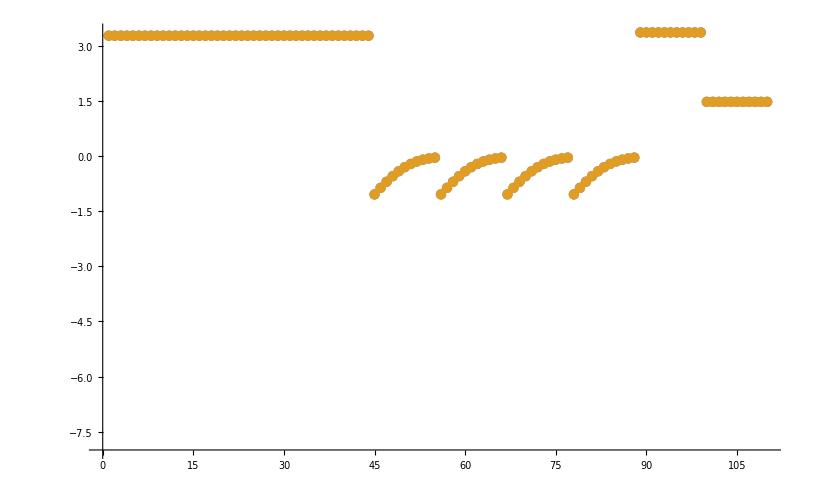

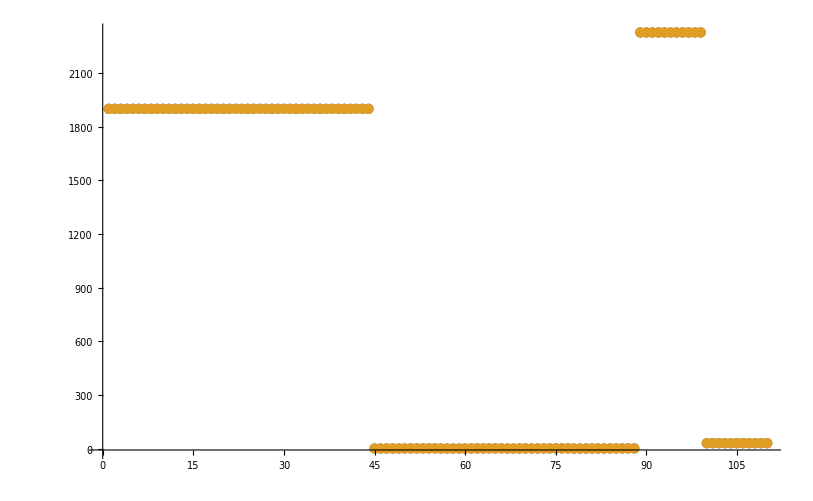

```mathematica
dataSetI=3;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

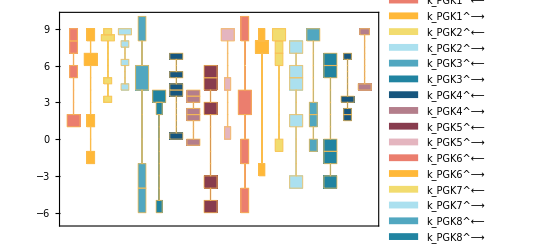

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

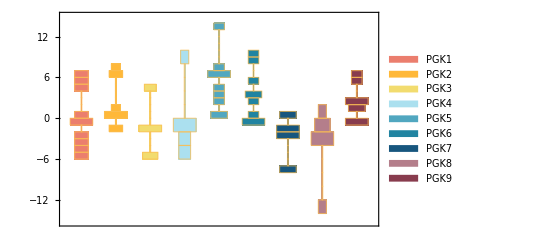

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

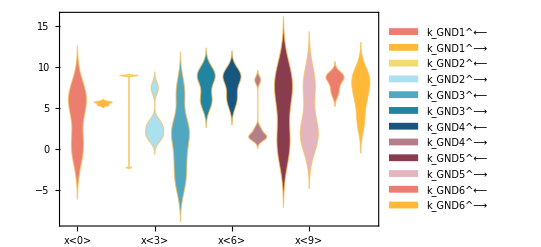

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

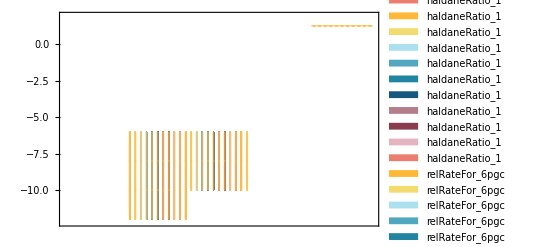

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

5.67233 | 6.08269 | 4.77434 | 6.06885 | 5.18744 | 3.43751 | 3.619 | 2.47805 | 2.437 | 8.47458 | 2.30999 | 7.46342 | 7.89166 | 5.31353 | 2.14299 | -1.04411 | 3.07099 | 4.22986

#### Parameter Cluster Plots (Optional)

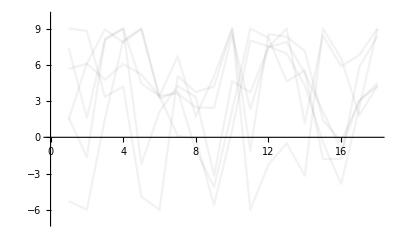

{-Graphics-}

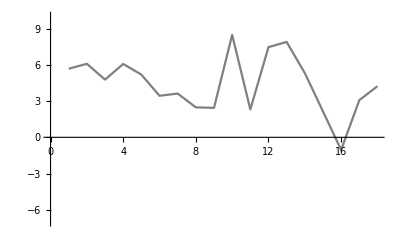

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000085 | 0.0000849964 | 0.00423497
0.000011 | 0.000011 | 0.000382447
0.0035 | 0.00349397 | 0.172288
0.0025 | 0.00249693 | 0.122993

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
2327.18 | 2327.18 | 0.000100621
30.0281 | 30.0281 | 0.000111743

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 9.90054×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 9.90054×10^-6

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,GND,«20»,{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]

## Export data

```mathematica
directoryExport = "C:\\Users\\Daniel Zielinski\\Desktop\\MASSpy Work\\"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\

CreateDirectory::filex: C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\rateconst_labels_pgk.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\S_pgk.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGK[c],E_PGK[c]&13dpg,E_PGK[c]&3pg,E_PGK[c]&adp,E_PGK[c]&atp,E_PGK[c]&13dpg&adp,13dpg[c],adp[c],atp[c],E_PGK[c]&3pg&atp,3pg[c]}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\species_pgk.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGK1: adp[c] + E_PGK[c] <=> E_PGK[c]&adp,PGK2: 13dpg[c] + E_PGK[c] <=> E_PGK[c]&13dpg,PGK3: E_PGK[c]&atp <=> atp[c] + E_PGK[c],PGK4: E_PGK[c]&3pg <=> 3pg[c] + E_PGK[c],PGK5: 13dpg[c] + E_PGK[c]&adp <=> E_PGK[c]&13dpg&adp,PGK6: adp[c] + E_PGK[c]&13dpg <=> E_PGK[c]&13dpg&adp,PGK7: E_PGK[c]&3pg&atp <=> 3pg[c] + E_PGK[c]&atp,PGK8: E_PGK[c]&3pg&atp <=> atp[c] + E_PGK[c]&3pg,PGK9: E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\reactions_pgk.txt

```mathematica
solEnz = Import["C:/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGK[c],E_PGK[c]&13dpg,E_PGK[c]&3pg,E_PGK[c]&adp,E_PGK[c]&atp,E_PGK[c]&13dpg&adp,E_PGK[c]&3pg&atp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((k_PGK3_fwd*(k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_PGK_total*param_Volume_c**5*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-(k_PGK2_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - adp(c)*k_PGK6_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)))))/((-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-(k_PGK2_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - adp(c)*k_PGK6_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))))*(k_PGK6_rev*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK9_rev*param_Volume_c**2*(-(3pg(c)*k_PGK4_rev*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)) - (k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) - (adp(c)*k_PGK1_fwd + 13dpg(c)*k_PGK2_fwd + atp(c)*k_PGK3_rev + 3pg(c)*k_PGK4_rev)*param_Volume_c))) - adp(c)*k_PGK1_fwd*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - 13dpg(c)*k_PGK2_fwd*param_Volume_c*(-(k_PGK5_rev*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - (k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**3 + (k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c))))) - (k_PGK6_rev*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK9_rev*param_Volume_c**2*(-(3pg(c)*k_PGK4_fwd*k_PGK4_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*param_Volume_c**3) - (k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c*(atp(c)*k_PGK3_fwd*k_PGK3_rev*param_Volume_c**2 - (adp(c)*k_PGK1_fwd + 13dpg(c)*k_PGK2_fwd + atp(c)*k_PGK3_rev + 3pg(c)*k_PGK4_rev)*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*param_Volume_c**2))) - adp(c)*k_PGK1_fwd*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) - 13dpg(c)*k_PGK2_fwd*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))))*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK2_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - adp(c)*k_PGK6_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-(k_PGK5_rev*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - (k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**3 + (k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))))))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\rateconst_clusters_pgk.txt

```mathematica
solRateEq = Import["C:/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\rateLaw_pgk.txt

### Sanity checking values of steady-state concentrations

```mathematica
solEnz[[1,1]]
solEnz[[1,2]]/.{Underscript[Volume, c]->1}
```

(PGK^c)_^

-((PGK_total_Global k_PGK3^⟶ (k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) k_PGK6^⟵ (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵ (-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) k_PGK6^⟵ (-adp^c k_PGK6^⟶ (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶)-k_PGK2^⟵ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)+(k_PGK2^⟵+adp^c k_PGK6^⟶) (-k_PGK5^⟵ (-(13dpg)^c k_PGK5^⟶ (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶)-k_PGK1^⟵ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶) (k_PGK5^⟵+k_PGK6^⟵+k_PGK9^⟶))))/((-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) k_PGK6^⟵ (-adp^c k_PGK6^⟶ (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶)-k_PGK2^⟵ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)+(k_PGK2^⟵+adp^c k_PGK6^⟶) (-k_PGK5^⟵ (-(13dpg)^c k_PGK5^⟶ (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶)-k_PGK1^⟵ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶) (k_PGK5^⟵+k_PGK6^⟵+k_PGK9^⟶))) (k_PGK6^⟵ (-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (-(3pg)^c k_PGK4^⟵ (-k_PGK3^⟶+k_PGK4^⟶)-(-adp^c k_PGK1^⟶-(13dpg)^c k_PGK2^⟶-atp^c k_PGK3^⟵-k_PGK3^⟶-(3pg)^c k_PGK4^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵)) k_PGK9^⟵-adp^c k_PGK1^⟶ (-(13dpg)^c k_PGK5^⟶ (k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-(-k_PGK3^⟶+k_PGK4^⟶) k_PGK8^⟶)-(k_PGK1^⟵-k_PGK3^⟶) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵))-(13dpg)^c k_PGK2^⟶ (-k_PGK5^⟵ (-(13dpg)^c k_PGK5^⟶ (k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-(-k_PGK3^⟶+k_PGK4^⟶) k_PGK8^⟶)-(k_PGK1^⟵-k_PGK3^⟶) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵+(k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-(-k_PGK3^⟶+k_PGK4^⟶) k_PGK8^⟶) (k_PGK5^⟵+k_PGK6^⟵+k_PGK9^⟶))))-(k_PGK6^⟵ (-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (-(3pg)^c k_PGK4^⟵ k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵)-(atp^c k_PGK3^⟵ k_PGK3^⟶-(adp^c k_PGK1^⟶+(13dpg)^c k_PGK2^⟶+atp^c k_PGK3^⟵+(3pg)^c k_PGK4^⟵) (k_PGK3^⟶+(3pg)^c k_PGK7^⟵)) (k_PGK4^⟶+atp^c k_PGK8^⟵)) k_PGK9^⟵-adp^c k_PGK1^⟶ (-(13dpg)^c k_PGK5^⟶ (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶)-k_PGK1^⟵ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵))-(13dpg)^c k_PGK2^⟶ (-k_PGK5^⟵ (-(13dpg)^c k_PGK5^⟶ (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶)-k_PGK1^⟵ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (-k_PGK3^⟶ k_PGK7^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-k_PGK4^⟶ (k_PGK3^⟶+(3pg)^c k_PGK7^⟵) k_PGK8^⟶) (k_PGK5^⟵+k_PGK6^⟵+k_PGK9^⟶))) (-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) k_PGK6^⟵ (-adp^c k_PGK6^⟶ (k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-(-k_PGK3^⟶+k_PGK4^⟶) k_PGK8^⟶)-(k_PGK2^⟵-k_PGK3^⟶) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)+(k_PGK2^⟵+adp^c k_PGK6^⟶) (-k_PGK5^⟵ (-(13dpg)^c k_PGK5^⟶ (k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-(-k_PGK3^⟶+k_PGK4^⟶) k_PGK8^⟶)-(k_PGK1^⟵-k_PGK3^⟶) (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵)-(k_PGK1^⟵+(13dpg)^c k_PGK5^⟶) (k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵) k_PGK9^⟵+(k_PGK3^⟶ (k_PGK4^⟶+atp^c k_PGK8^⟵)-(-k_PGK3^⟶+k_PGK4^⟶) k_PGK8^⟶) (k_PGK5^⟵+k_PGK6^⟵+k_PGK9^⟶))))))

```mathematica
rateConstsSub[[All,1]]
filteredDataList[[1,2]]
rateSubTest = Thread[rateConstsSub[[All,1]]->filteredDataList[[1,2]]]
```

{k_PGK1^⟵,k_PGK1^⟶,k_PGK2^⟵,k_PGK2^⟶,k_PGK3^⟵,k_PGK3^⟶,k_PGK4^⟵,k_PGK4^⟶,k_PGK5^⟵,k_PGK5^⟶,k_PGK6^⟵,k_PGK6^⟶,k_PGK7^⟵,k_PGK7^⟶,k_PGK8^⟵,k_PGK8^⟶,k_PGK9^⟵,k_PGK9^⟶}

{2.26778×10^7,40.8226,1.13622×10^8,9.99999×10^8,28346.4,2629.52,1.33668,0.760767,2.49086×10^-6,4.02222,1.02678×10^8,3.39124×10^7,8.80601×10^6,20259.4,0.377452,0.000141535,302.948,9.27852×10^8}

{k_PGK1^⟵→2.26778×10^7,k_PGK1^⟶→40.8226,k_PGK2^⟵→1.13622×10^8,k_PGK2^⟶→9.99999×10^8,k_PGK3^⟵→28346.4,k_PGK3^⟶→2629.52,k_PGK4^⟵→1.33668,k_PGK4^⟶→0.760767,k_PGK5^⟵→2.49086×10^-6,k_PGK5^⟶→4.02222,k_PGK6^⟵→1.02678×10^8,k_PGK6^⟶→3.39124×10^7,k_PGK7^⟵→8.80601×10^6,k_PGK7^⟶→20259.4,k_PGK8^⟵→0.377452,k_PGK8^⟶→0.000141535,k_PGK9^⟵→302.948,k_PGK9^⟶→9.27852×10^8}

```mathematica
metSubTest = {(13dpg)^c->1,adp^c->1,(3pg)^c-> 0,atp^c-> 0}
```

{(13dpg)^c→1,adp^c→1,(3pg)^c→0,atp^c→0}

#### Steady-state concentration of individual enzyme forms

```mathematica
solEnz[[1,1]]
solEnz[[1,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest

solEnz[[2,1]]
solEnz[[2,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest

solEnz[[3,1]]
solEnz[[3,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest

solEnz[[4,1]]
solEnz[[4,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest

solEnz[[5,1]]
solEnz[[5,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest

solEnz[[6,1]]
solEnz[[6,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest

solEnz[[7,1]]
solEnz[[7,2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest
```

(PGK^c)_^

0.0000110001

(PGK^c&(13dpg)^c)_^

0.0000763308

(PGK^c&(3pg)^c)_^

0.0000213705

(PGK^c&adp^c)_^

1.98014×10^-11

(PGK^c&atp^c)_^

0.88502

(PGK^c&(13dpg)^c&adp^c)_^

2.54564×10^-6

(PGK^c&(3pg)^c&atp^c)_^

0.114869

#### Steady-state flux equation

```mathematica
solRateEq[[2]]/.{Underscript[Volume, c]->1,Underscript[PGK_total, Global]->1}/.rateSubTest/.metSubTest
```

2327.18

```mathematica
2327.1762492104904*3600
```

8.37783×10^6

#### Check if plugging in enzyme forms and other concentrations yields a steady-state flux

```mathematica
"E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp"
```

```mathematica
metSubTest2 = {(PGK^c&(13dpg)^c&adp^c)_^-> 2.545638782760162*^-6, (PGK^c&(3pg)^c&atp^c)_^-> 0.11486891255476626};
rateSubTest2 = {Subscript[k, PGK9]^⟶-> 9.278517941052091*^8,Subscript[k, PGK9]^⟵-> 302.9476099607256};
```

```mathematica
fluxSsCheck = ((PGK^c&(13dpg)^c&adp^c)_^*Subscript[k, PGK9]^⟶-(PGK^c&(3pg)^c&atp^c)_^*Subscript[k, PGK9]^⟵)/.metSubTest2/.rateSubTest2
```

2327.18

```mathematica
enzymeModel
```